```mathematica
M0=0.7
```

0.7

```mathematica
rb=2/M0
```

2.85714

```mathematica
3*(3)^0.5*(M0*rb/2)
```

5.19615

```mathematica
Aint=(1-M0)*(r/rb)^(M0/(1-M0))
```

0.0258988 r^2.33333

```mathematica
Aext=(1-(M0*rb/r))
```

1-2./r

```mathematica
Bint=1/(1-M0)
```

3.33333

```mathematica
Bext=(1-(M0*rb/r))^(-1)
```

1/(1-2./r)

```mathematica
krtint=((Aint/Bint)*(1-(b^2Aint/(r^2))))^0.5
```

0.0881456 ((1-0.0258988 b^2 r^0.333333) r^2.33333)^0.5

```mathematica
krtext=((Aext/Bext)*(1-(b^2Aext/(r^2))))^0.5
```

((1-(b^2 (1-2./r))/r^2) (1-2./r)^2)^0.5

```mathematica
gintredshift=((1/Aint)+krtint*(Bint/Aint)*((1-Aint)/(Aint*Bint))^0.5)^(-1)
```

1/(38.6118/r^2.33333+(38.6118 ((1-0.0258988 b^2 r^0.333333) r^2.33333)^0.5 ((1-0.0258988 r^2.33333)/r^2.33333)^0.5)/r^2.33333)

```mathematica
greddhift=((1/Aext)+krtext*(Bext/Aext)*((1-Aext)/(Aext*Bext))^0.5)^(-1)
```

1/(1/(1-2./r)+(1.41421 ((1-(b^2 (1-2./r))/r^2) (1-2./r)^2)^0.5 (1/r)^0.5)/(1-2./r)^2)

```mathematica
gblueshift=((1/Aext)-krtext*(Bext/Aext)*((1-Aext)/(Aext*Bext))^0.5)^(-1)
```

1/(1/(1-2./r)-(1.41421 ((1-(b^2 (1-2./r))/r^2) (1-2./r)^2)^0.5 (1/r)^0.5)/(1-2./r)^2)

```mathematica
IntredshiftJMN:=(gintredshift^3)*(Aint/(r^2))*(1/krtint)
```

```mathematica
Intblueshift:=-(gblueshift^3)*(Aext/(r^2))*(1/krtext)
```

```mathematica
Intredshift:=(greddhift^3)*(Aext/(r^2))*(1/krtext)
```

```mathematica
data1:=Table[{b,Re[NIntegrate[Intblueshift,{r,50,r/.NSolve[r/(Aext)^(0.5)==b,r][[1]]}]+NIntegrate[Intredshift,{r,r/.NSolve[r/(Aext)^(0.5)==b,r][[1]],50}]]},{b,5.196152422706632,40,0.05}]
```

```mathematica
data2:=Table[{b,Re[NIntegrate[IntredshiftJMN,{r,0,rb}]+NIntegrate[Intredshift,{r,rb,50}]]},{b,0.001,5.196152422706632,0.05}]
```

```mathematica
data2re:=Table[{-b,Re[NIntegrate[IntredshiftJMN,{r,0,rb}]+NIntegrate[Intredshift,{r,rb,50}]]},{b,0.001,5.196152422706632,0.05}]
```

```mathematica
data1re:=Table[{-b,Re[NIntegrate[Intblueshift,{r,50,r/.NSolve[r/(Aext)^(0.5)==b,r][[1]]}]+NIntegrate[Intredshift,{r,r/.NSolve[r/(Aext)^(0.5)==b,r][[1]],50}]]},{b,5.196152422706632,40,0.05}]
```

```mathematica
Dataeff1:=Join[data2,data1]
Dataeff2:=Join[data2re,data1re]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {3.0000008703818239672692587730572222337599441743805073201656341553}. NIntegrate obtained 0.626917-0.00121288 ⅈ and 0.00353088 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {3.0000008703818239672692587730572222337599441743805073201656341553}. NIntegrate obtained 0.182241-0.00121288 ⅈ and 0.00353084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {3.0000008703818239672692587730572222337599441743805073201656341553}. NIntegrate obtained 0.626917-0.00121288 ⅈ and 0.00353088 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

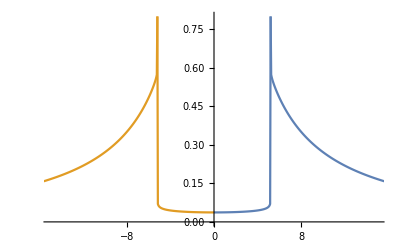

```mathematica
ListLinePlot[{Dataeff1,Dataeff2},PlotRange->{{-15,15},{0,0.8}}]
```

```mathematica
Show[%22,AxesLabel->{HoldForm[b],HoldForm[intensity]},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0],Bold}]
```

```mathematica
Intblueshift
```

-(1-2./r)/((1/(1-2./r)-(1.41421 ((1-(b^2 (1-2./r))/r^2) (1-2./r)^2)^0.5 (1/r)^0.5)/(1-2./r)^2)^3 ((1-(b^2 (1-2./r))/r^2) (1-2./r)^2)^0.5 r^2)

```mathematica
Intredshift
```

(1-2./r)/((1/(1-2./r)+(1.41421 ((1-(b^2 (1-2./r))/r^2) (1-2./r)^2)^0.5 (1/r)^0.5)/(1-2./r)^2)^3 ((1-(b^2 (1-2./r))/r^2) (1-2./r)^2)^0.5 r^2)

```mathematica
Intensityobssch:=Table[With[{b=RandomReal[{5.196152422706632,15}],t=RandomReal[{0,2 Pi}]},{b*Cos[t],b* Sin[t],NIntegrate[-(1-2./r)/((1/(1-2./r)-(1.4142135623730951 ((1-(b^2 (1-2./r))/r^2) (1-2./r)^2)^0.5 (1/r)^0.5)/(1-2./r)^2)^3 ((1-(b^2 (1-2./r))/r^2) (1-2./r)^2)^0.5 r^2),{r,50,r/.NSolve[r/(Aext)^(0.5)==b,r][[1]]}]+NIntegrate[(1-2./r)/((1/(1-2./r)+(1.4142135623730951 ((1-(b^2 (1-2./r))/r^2) (1-2./r)^2)^0.5 (1/r)^0.5)/(1-2./r)^2)^3 ((1-(b^2 (1-2./r))/r^2) (1-2./r)^2)^0.5 r^2),{r,r/.NSolve[r/(Aext)^(0.5)==b,r][[1]],50}]}],{10^4}];
```

```mathematica
IntredshiftJMN
```

(0.293819 r^0.333333)/(((1-0.0258988 b^2 r^0.333333) r^2.33333)^0.5 (38.6118/r^2.33333+(38.6118 ((1-0.0258988 b^2 r^0.333333) r^2.33333)^0.5 ((1-0.0258988 r^2.33333)/r^2.33333)^0.5)/r^2.33333)^3)

```mathematica
Intensityobsint:=Table[With[{b=RandomReal[{0.01,5.196152422706632}],t=RandomReal[{0,2 Pi}]},{b*Cos[t],b* Sin[t],Re[NIntegrate[(0.29381866766390957 r^0.33333333333333304)/(((1-0.025898822840338485 b^2 r^0.33333333333333304) r^2.333333333333333)^0.5 (38.611793523003634/r^2.333333333333333+(38.61179352300364 ((1-0.025898822840338485 b^2 r^0.33333333333333304) r^2.333333333333333)^0.5 ((1-0.025898822840338485 r^2.333333333333333)/r^2.333333333333333)^0.5)/r^2.333333333333333)^3),{r,0,rb}]+NIntegrate[(1-2./r)/((1/(1-2./r)+(1.4142135623730951 ((1-(b^2 (1-2./r))/r^2) (1-2./r)^2)^0.5 (1/r)^0.5)/(1-2./r)^2)^3 ((1-(b^2 (1-2./r))/r^2) (1-2./r)^2)^0.5 r^2),{r,rb,50}]]}],{10^4}];
```

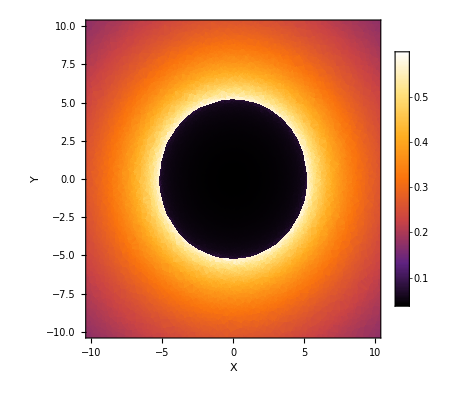

```mathematica
ListDensityPlot[{Intensityobssch,Intensityobsint},PlotRange->{{-10,10},{-10,10}},ColorFunction->"SunsetColors",PlotLegends->Automatic,FrameLabel->{{HoldForm[Y],None},{HoldForm[X],None}},PlotLabel->None,LabelStyle->{12,GrayLevel[0],Bold}]
```

```mathematica
itt:=Table[{b,Re[NIntegrate[IntredshiftJMN,{r,0,2}]+NIntegrate[Intredshift,{r,2,50}]]},{b,0.001,5.196152422706632,0.05}]
```

```mathematica
itt2:=Table[{-b,Re[NIntegrate[IntredshiftJMN,{r,0,2}]+NIntegrate[Intredshift,{r,2,50}]]},{b,0.001,5.196152422706632,0.05}]
```

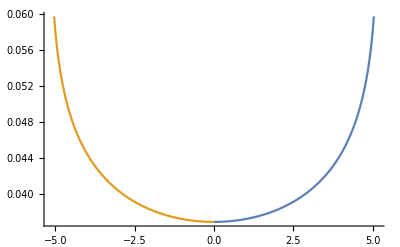

```mathematica
ListLinePlot[{itt,itt2}]
```

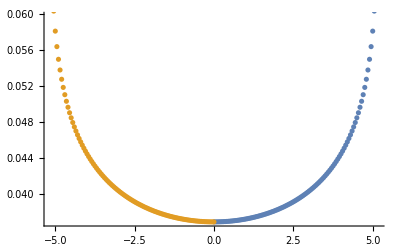

```mathematica
ListPlot[{itt,itt2}]
```

```mathematica
Intensityjjj:=Table[With[{b=RandomReal[{0.01,5.196152422706632}],t=RandomReal[{0,2 Pi}]},{b*Cos[t],b* Sin[t],Re[NIntegrate[(0.29381866766390957 r^0.33333333333333304)/(((1-0.025898822840338485 b^2 r^0.33333333333333304) r^2.333333333333333)^0.5 (38.611793523003634/r^2.333333333333333+(38.61179352300364 ((1-0.025898822840338485 b^2 r^0.33333333333333304) r^2.333333333333333)^0.5 ((1-0.025898822840338485 r^2.333333333333333)/r^2.333333333333333)^0.5)/r^2.333333333333333)^3),{r,0,2}]+NIntegrate[(1-2./r)/((1/(1-2./r)+(1.4142135623730951 ((1-(b^2 (1-2./r))/r^2) (1-2./r)^2)^0.5 (1/r)^0.5)/(1-2./r)^2)^3 ((1-(b^2 (1-2./r))/r^2) (1-2./r)^2)^0.5 r^2),{r,2,50}]]}],{10^4}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {3.03413578501252}. NIntegrate obtained 0.0975272 and 1.87801×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {3.03413578501252}. NIntegrate obtained 0.12663 and 0.00746935 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {3.03413578501252}. NIntegrate obtained 0.092442 and 1.28163×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

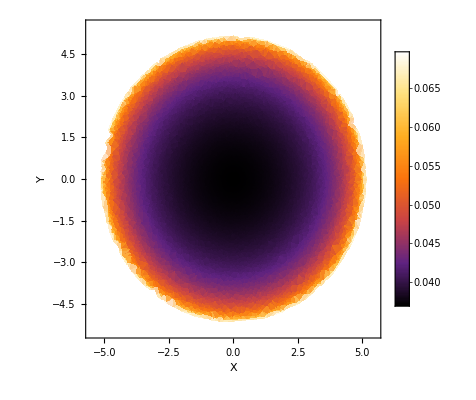

```mathematica
ListDensityPlot[{Intensityjjj},PlotRange->{{-5.5,5.5},{-5.5,5.5}},ColorFunction->"SunsetColors",PlotLegends->Automatic,FrameLabel->{{HoldForm[Y],None},{HoldForm[X],None}},PlotLabel->None,LabelStyle->{12,GrayLevel[0],Bold}]
```